# Метод на допирателните (Нютон)

## Задача 1:

Дадено е уравнението:
(x^3 + px - (q + 50)sin3x  -2(p + q))/((x-1)(x+2))= 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер.
(x^3 + x -58sin3x  -16)/((x-1)(x+2))= 0
=> Допустима област : 
x - 1 != 0  => x !=  1
x + 2 != 0 => x != -2
1. Да се намери общия брой на корените на уравнението.
2. Да се локализира най-големия реален корен в интервал [a, b].
3. Да се проверят условията за приложение на метода на допирателните (Нютон).
4. Да се определи началното приближение за итерационния процес по метода на допирателните (Нютон).
5. Да се изчисли корена по метода на допирателните с точност 10^-7. Представете таблица с изчисленията.
6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
7. Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := (x^3 + x - 58Sin[3x] - 16)/((x-1)(x+2))
```

```mathematica
f[x]
```

(-16+x+x^3-58 Sin[3 x])/((-1+x) (2+x))

## 1. Да се намери общия брой на корените на уравнението

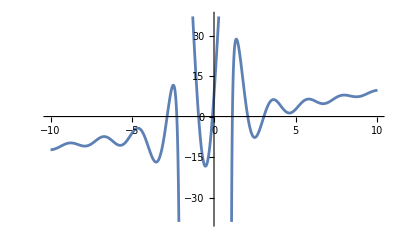

```mathematica
Plot[f[x], {x, -10, 10}]
```

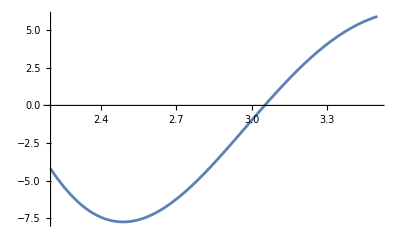

```mathematica
Plot[f[x], {x, 2.2, 3.5}]
```

Брой корени: 7

## 2. Да се локализира най-големия реален корен в интервала [a, b]

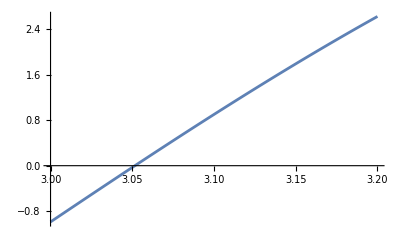

```mathematica
Plot[f[x], {x, 3., 3.2}]
```

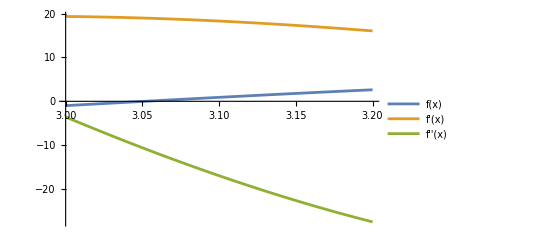

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, 3., 3.2}, PlotLegends -> "Expressions" ]
```

```mathematica
f[3.]
```

-0.990287

```mathematica
f[3.2]
```

2.62928

Извод:
1. f(3.55) = -0.990287 < 0
2. f(4) = 2.62928 > 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [3.;3.2]. Следва, че функцията има поне един корен в дадения интервал.

## 3. Проверка на условията за сходимост

### Проверка на първата производна

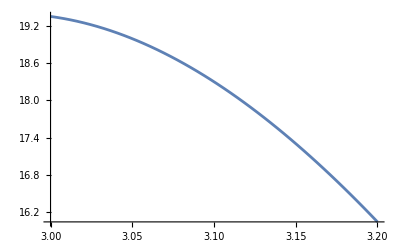

```mathematica
Plot[f'[x], {x, 3., 3.2}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [3.; 3.2] са между 16 и 19. Следователно първата f’(x) > 0 в целия разглеждан интервал [3.; 3.2].

### Проверка на втората производна

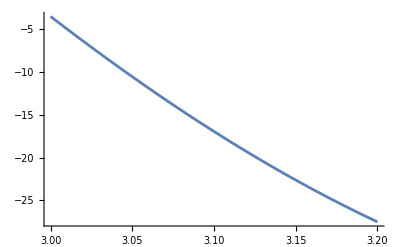

```mathematica
Plot[f''[x],{x, 3., 3.2}]
```

Извод: (2) Стойностите на втората производна в разглеждания интервал [3.; 3.2] са между -3 и -27. Следователно втората прозв. f’’(x) < 0 в целия разглеждан интервал [3.; 3.2].

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [3.; 3.2] => Методът на допирателните е сходящ.

## 4. Избор на начално приближение

f’’ < 0 за текущата задача. Следователно избираме x0 , така че f(x_0).f’’ > 0.

=> f(x_0) < 0
=> x_0 = 3

```mathematica
x0 =3
```

3

### Пресмятане на постоянните величини:

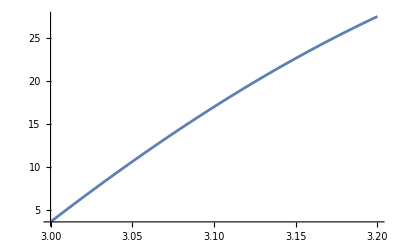

```mathematica
Plot[Abs[f''[x]], {x, 3., 3.2}]
```

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
М2 = Abs[f''[3.2]]
```

27.4983

```mathematica
Plot[Abs[f'[x]], {x, 3., 3.2}]
```

-Graphics-

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия .

```mathematica
m1 = Abs[f'[3.]]
```

19.3469

```mathematica
p = М2/(2m1)
```

0.710665

## 5.Да се изчисли корена по метода на допирателните с точност 10^-7

```mathematica
f[x_] := (x^3 + x - 58Sin[3x] - 16)/((x-1)(x+2))
x0 = 4;
М2 = Abs[f''[3.55]];
m1 = Abs[f'[3.55]];
p = М2/(2m1);
epszad = 0.0000001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x) = ", f[x0], " f'(x) = ", f'[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1] " f'(x_n) = ", f'[x1], " ε_n = ", eps = p* (x1 - x0)^2];
x0 = x1
]
```

n = 0 x_n = 3.55 f(x) = -0.0296069 f'(x) = 0.0247471

n = 1 x_n = 4.74638 f(x_n) = 6.02116  f'(x_n) = -0.1078 ε_n = 0.418908

n = 2 x_n = 60.6016 f(x_n) = 59.7357  f'(x_n) = 1.02976 ε_n = 913.084

n = 3 x_n = 2.59228 f(x_n) = 6.81679  f'(x_n) = -0.828207 ε_n = 984.87

n = 4 x_n = 10.8231 f(x_n) = 10.6707  f'(x_n) = 1.42574 ε_n = 19.8274

n = 5 x_n = 3.33868 f(x_n) = 0.582997  f'(x_n) = -5.7776 ε_n = 16.3944

n = 6 x_n = 3.43959 f(x_n) = 0.136306  f'(x_n) = -3.04257 ε_n = 0.00298003

n = 7 x_n = 3.48439 f(x_n) = 0.0280431  f'(x_n) = -1.79013 ε_n = 0.000587398

n = 8 x_n = 3.50005 f(x_n) = 0.00342653  f'(x_n) = -1.3529 ε_n = 0.0000718235

n = 9 x_n = 3.50258 f(x_n) = 0.0000893427  f'(x_n) = -1.28235 ε_n = 1.87743×10^-6

n = 10 x_n = 3.50265 f(x_n) = 6.75728×10^-8  f'(x_n) = -1.28041 ε_n = 1.42065×10^-9

## 6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност

```mathematica
Log2[(4 - 3.55)/0.0000001] - 1
```

21.1015

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 10 итерации за достигане на исканата точност. А по метода на разполовяването са необходими 22 итерации. Следователно методът на допирателните е по-ефективен за избрания интервал [3.55, 4].

## Задача 2:

Дадено е уравнението:
x^2 - 33sin(x + π/(p + 1)) - (p + 2q)= 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер.
x^2 - 33sin(x + π/1) - 16 = 0
1. Да се намери общия брой на корените на уравнението.
2. Да се локализира най-малкия реален корен в интервал [a, b].
3. Да се проверят условията за приложение на метода на допирателните (Нютон).
4. Да се определи началното приближение за итерационния процес по метода на допирателните (Нютон).
5. Да се изчисли корена по метода на допирателните с точност 0,0000000001. Представете таблица с изчисленията.
6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
7. Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := x^2 - 33Sin[x + π/1] - 16
```

```mathematica
f[x]
```

-16+x^2+33 Sin[x]

## 1. Да се намери общия брой на корените на уравнението.

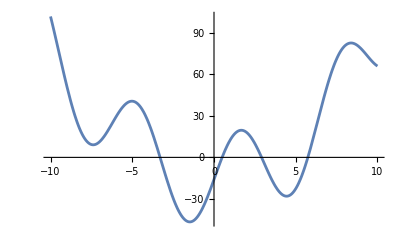

```mathematica
Plot[f[x], {x, -10, 10}]
```

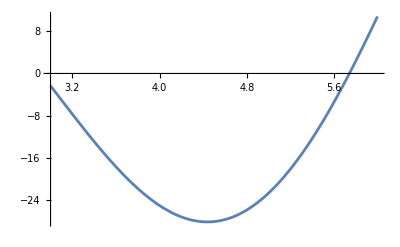

```mathematica
Plot[f[x], {x, 3, 6}]
```

Брой корени: 4

## 2. Да се локализира най-малкия реален корен в интервал [a, b].

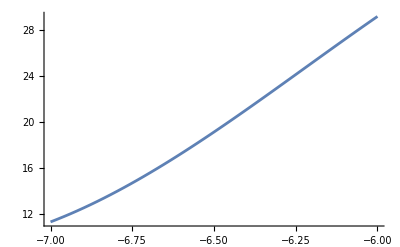

```mathematica
Plot[f[x], {x, -7, -6}]
```

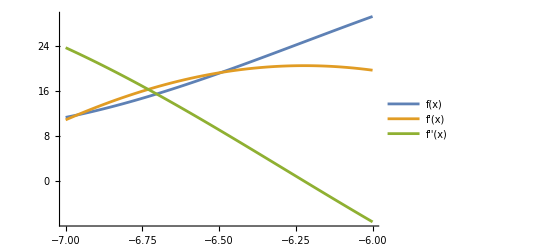

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -7, -6}, PlotLegends->"Expressions"]
```

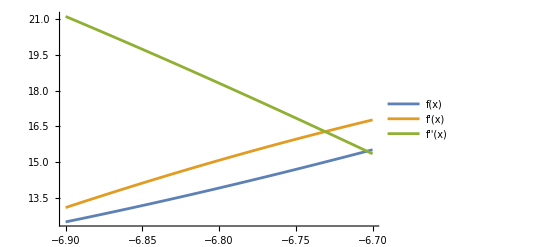

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -6.9, -6.7}, PlotLegends->"Expressions"]
```

```mathematica
f[-6.9]
```

12.5215

```mathematica
f[-6.7]
```

15.53

Извод:
1. f(-6.9) = 12.5215 > 0
2. f(-6.7) = 15.53 < 0

## 3. Проверка на условията за сходимост

### Проверка на първата производна

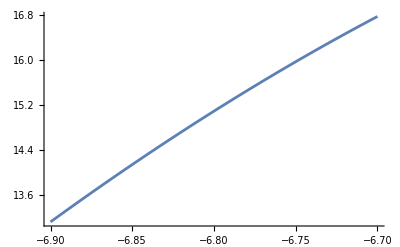

```mathematica
Plot[f'[x], {x, -6.9, -6.7}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-6.9; -6.7] са между 13 и 16. Следователно първата f’(x) > 0 в целия разглеждан интервал [-6.9; -6.7].

### Проверка на втората производна

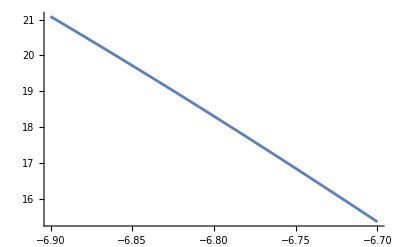

```mathematica
Plot[f''[x], {x, -6.9, -6.7}]
```

Извод: (2) Стойностите на първата производна в разглеждания интервал [-6.9; -6.7] са между 15 и 21. Следователно втората f''(x) > 0 в целия разглеждан интервал [-6.9; -6.7].

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [-6.9; -6.7] => Методът на допирателните е сходящ.

## 4. Избор на начално приближение

f’’ > 0 за текущата задача. Следователно избираме x0 , така че f(x_0).f’’ > 0.
=> f(x_0) > 0
=> x_0 = -6.9

### Пресмятане на постоянните величини:

```mathematica
Plot[Abs[f''[x]], {x, -6.9, -6.7}]
```

-Graphics-

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
М2 = Abs[f''[-6.9]]
```

21.0885

```mathematica
Plot[Abs[f'[x]], {x, -6.9, -6.7}]
```

-Graphics-

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
m1 = Abs[f'[-6.7]]
```

16.7746

```mathematica
p = М2/(2m1)
```

0.628583

## 5.Да се изчисли корена по метода на допирателните с точност 0,0000000001

```mathematica
f[x_] := x^2 - 33Sin[x + π/1] - 16
x0 = -6.9;
М2 = Abs[f''[-6.9]];
m1 = Abs[f'[-6.7]];
p = М2/(2m1);
epszad = 0.0000000001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x) = ", f[x0], " f'(x) = ", f'[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1] " f'(x_n) = ", f'[x1], " ε_n = ", eps = p* (x1 - x0)^2];
x0 = x1
]
```

n = 0 x_n = -6.9 f(x) = 12.5215 f'(x) = 13.1189

n = 1 x_n = -7.85446 f(x_n) = 12.6925  f'(x_n) = -15.7247 ε_n = 0.572635

n = 2 x_n = -7.04729 f(x_n) = 10.8319  f'(x_n) = 9.73156 ε_n = 0.409539

n = 3 x_n = -8.16036 f(x_n) = 19.1282  f'(x_n) = -26.2737 ε_n = 0.77877

n = 4 x_n = -7.43232 f(x_n) = 9.12985  f'(x_n) = -1.35864 ε_n = 0.333171

n = 5 x_n = -0.712485 f(x_n) = -37.065  f'(x_n) = 23.5474 ε_n = 28.3845

n = 6 x_n = 0.861571 f(x_n) = 9.7849  f'(x_n) = 23.2143 ε_n = 1.55741

n = 7 x_n = 0.440067 f(x_n) = -1.74833  f'(x_n) = 30.736 ε_n = 0.111677

n = 8 x_n = 0.496949 f(x_n) = -0.020417  f'(x_n) = 30.0023 ε_n = 0.00203384

n = 9 x_n = 0.49763 f(x_n) = -3.18131×10^-6  f'(x_n) = 29.9929 ε_n = 2.91097×10^-7

n = 10 x_n = 0.49763 f(x_n) = -6.92779×10^-14  f'(x_n) = 29.9929 ε_n = 7.07194×10^-15

## 6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност

```mathematica
Log2[(-6.7 + 6.9)/0.0000000001] - 1
```

29.8974

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 4 итерации за достигане на исканата точност. А по метода на разполовяването са необходими 30 итерации. Следователно методът на допирателните е по-ефективен за избрания интервал [-6.9, -6.7].